β | 200 | 190 | 180 | 170 | 160 | 150 | 140 | 130 | 125 | 120 | 115 | 110 | 105 | 100 | 95 | 90 | 85 | 80
C_β | 1.04 | 1.02 | 1 | 0.97 | 0.95 | 0.92 | 0.89 | 0.86 | 0.84 | 0.82 | 0.8 | 0.78 | 0.76 | 0.74 | 0.72 | 0.68 | 0.66 | 0.64

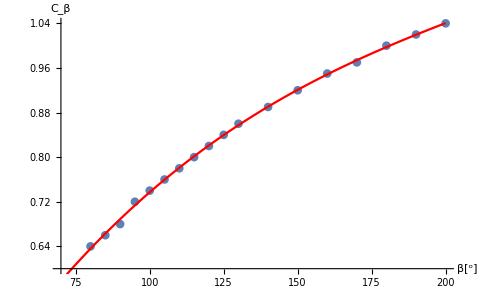

Interpolacioni polinom ima sledeci oblik: y=0.00281601+0.0106648 x-0.0000390555 x^2+5.83701×10^-8 x^3

```mathematica
(*Faktor obvojnog ugla trapeznih i rebrastih remena Subscript[C, β]*)
(*Tabela 10.12 - str. 385 - Milcic.*)
SetOptions[ListPlot,BaseStyle->{FontFamily->"Century Schoolbook",FontSize->16}];
(*Definisanje uredjene liste podataka*)
Lista={{200,1.04},{190,1.02},{180,1},{170,0.97},{160,0.95},{150,0.92},{140,0.89},{130,0.86},{125,0.84},{120,0.82},{115,0.8},{110,0.78},{105,0.76},{100,0.74},{95,0.72},{90,0.68},{85,0.66},{80,0.64}};

Grid[{{β,200,190,180,170,160,150,140,130,125,120,115,110,105,100,95,90,85,80},{Subscript[C, β],1.04,1.02,1,0.97,0.95,0.92,0.89,0.86,0.84,0.82,0.8,0.78,0.76,0.74,0.72,0.68,0.66,0.64}},Frame->All]

(*Fitovanje*)
Fitovanje=Fit[Lista,{1,x,x^2,x^3},x];

(*Stampanje funkcije*)
Grafik1=ListPlot[Lista,AxesOrigin->{70,0.6},AxesLabel->{"β[^o]","C_β"}];
Grafik2=Plot[Fitovanje,{x,70,200},PlotStyle->Red];
Show[Grafik1,Grafik2]
Print["Interpolacioni polinom ima sledeci oblik: y=", Fitovanje]
F[x_]=Fitovanje;
```

```mathematica
(*Procentualna greska interpolacionog polinoma*)
```

```mathematica
Greska=Abs[F[90]-0.68]/0.68*100
```

1.30094

```mathematica
F[167.288]
```

0.967188